```mathematica
Clear["Global`*"]  (*Clear all variables*)
d = 1;
lam = 5;
k=Range[-5/lam*2*Pi,5/lam*2*Pi,0.05/lam*2*Pi];
y_d1=Abs[NIntegrate[Exp[I 2 Pi *Sqrt[x^2+d^2]/lam]/(2 lam Sqrt[x^2+d^2])  (d^2/(x^2+d^2)  + (I (d^2-2x^2))/((2 Pi/ lam)  *Sqrt[x^2+d^2]^3) -(d^2-2x^2)/((2 Pi/ lam)^2  *(x^2+d^2)^2)) Exp[I k x],{x,-∞,∞}]]
d = 5;
k=Range[-5/lam*2*Pi,5/lam*2*Pi,0.05/lam*2*Pi];
y_d5=Abs[NIntegrate[Exp[I 2 Pi *Sqrt[x^2+d^2]/lam]/(2 lam Sqrt[x^2+d^2])  (d^2/(x^2+d^2)  + (I (d^2-2x^2))/((2 Pi/ lam)  *Sqrt[x^2+d^2]^3) -(d^2-2x^2)/((2 Pi/ lam)^2  *(x^2+d^2)^2)) Exp[I k x],{x,-∞,∞}]]
d = 20;
k=Range[-5/lam*2*Pi,5/lam*2*Pi,0.05/lam*2*Pi];
y_d20=Abs[NIntegrate[Exp[I 2 Pi *Sqrt[x^2+d^2]/lam]/(2 lam Sqrt[x^2+d^2])  (d^2/(x^2+d^2)  + (I (d^2-2x^2))/((2 Pi/ lam)  *Sqrt[x^2+d^2]^3) -(d^2-2x^2)/((2 Pi/ lam)^2  *(x^2+d^2)^2)) Exp[I k x],{x,-∞,∞}]]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.81037×10^7}. NIntegrate obtained -4.44692×10^-19+6.50521×10^-18 ⅈ and 2.65435×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-4.81037×10^7}. NIntegrate obtained -3.81638×10^-12+3.67414×10^-15 ⅈ and 3.09571×10^-13 for the integral and error estimates.

{0.00504456,0.0052939,0.00555473,0.00582753,0.00611277,0.00641096,0.00672259,0.0070482,0.00738831,0.00774349,0.00811429,0.00850129,0.00890509,0.00932627,0.00976544,0.0102232,0.0107003,0.0111972,0.0117146,0.0122532,0.0128137,0.0133965,0.0140025,0.0146323,0.0152864,0.0159655,0.0166702,0.0174012,0.0181589,0.0189438,0.0197566,0.0205977,0.0214674,0.0223662,0.0232944,0.0242521,0.0252395,0.0262567,0.0273036,0.02838,0.0294858,0.0306203,0.031783,0.0329731,0.0341895,0.0354311,0.0366963,0.0379833,0.03929,0.040614,0.0419524,0.0433019,0.0446586,0.0460183,0.0473759,0.0487259,0.0500617,0.0513761,0.0526607,0.0539063,0.055102,0.0562357,0.0572937,0.0582601,0.0591169,0.0598432,0.0604151,0.0608045,0.0609786,0.0608984,0.0605171,0.0597776,0.0586088,0.0569198,0.0545913,0.051459,0.0472847,0.0416928,0.0340137,0.0227443,6.52039×10^-18,0.035048,0.0596984,0.0805064,0.0987392,0.114977,0.129551,0.142677,0.154502,0.165136,0.17466,0.183137,0.190618,0.197142,0.202741,0.20744,0.21126,0.214216,0.216319,0.217578,0.217997,0.217578,0.216319,0.214216,0.21126,0.20744,0.202741,0.197142,0.190618,0.183137,0.17466,0.165136,0.154502,0.142677,0.129551,0.114977,0.0987392,0.0805064,0.0596984,0.035048,3.81638×10^-12,0.0227443,0.0340137,0.0416928,0.0472847,0.051459,0.0545913,0.0569198,0.0586088,0.0597776,0.0605171,0.0608984,0.0609786,0.0608045,0.0604151,0.0598432,0.0591169,0.0582601,0.0572937,0.0562357,0.055102,0.0539063,0.0526607,0.0513761,0.0500617,0.0487259,0.0473759,0.0460183,0.0446586,0.0433019,0.0419524,0.040614,0.03929,0.0379833,0.0366963,0.0354311,0.0341895,0.0329731,0.031783,0.0306203,0.0294858,0.02838,0.0273036,0.0262567,0.0252395,0.0242521,0.0232944,0.0223662,0.0214674,0.0205977,0.0197566,0.0189438,0.0181589,0.0174012,0.0166702,0.0159655,0.0152864,0.0146323,0.0140025,0.0133965,0.0128137,0.0122532,0.0117146,0.0111972,0.0107003,0.0102232,0.00976544,0.00932627,0.00890509,0.00850129,0.00811429,0.00774349,0.00738831,0.0070482,0.00672259,0.00641096,0.00611277,0.00582753,0.00555473,0.0052939,0.00504456}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-11.8403}. NIntegrate obtained -4.62724×10^-14-1.56532×10^-18 ⅈ and 1.18487×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {6.83186}. NIntegrate obtained -6.27738×10^-14-8.94467×10^-19 ⅈ and 1.27281×10^-16 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-12.838}. NIntegrate obtained -8.51422×10^-14-2.88838×10^-19 ⅈ and 1.18404×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

{4.62724×10^-14,6.27738×10^-14,8.51422×10^-14,1.15503×10^-13,1.56673×10^-13,2.12503×10^-13,2.8823×10^-13,3.90911×10^-13,5.30156×10^-13,7.18999×10^-13,9.75071×10^-13,1.3223×10^-12,1.79311×10^-12,2.43152×10^-12,3.29712×10^-12,4.47076×10^-12,6.06201×10^-12,8.21943×10^-12,1.11444×10^-11,1.51101×10^-11,2.04865×10^-11,2.77755×10^-11,3.76575×10^-11,5.10548×10^-11,6.9218×10^-11,9.38425×10^-11,1.27227×10^-10,1.72489×10^-10,2.33855×10^-10,3.17056×10^-10,4.29865×10^-10,5.82824×10^-10,7.90232×10^-10,1.07148×10^-9,1.45289×10^-9,1.97016×10^-9,2.67173×10^-9,3.62335×10^-9,4.91427×10^-9,6.66565×10^-9,9.04203×10^-9,1.22669×10^-8,1.66438×10^-8,2.25855×10^-8,3.06527×10^-8,4.16082×10^-8,5.64896×10^-8,7.6709×10^-8,1.04189×10^-7,1.41549×10^-7,1.92359×10^-7,2.61489×10^-7,3.55586×10^-7,4.83727×10^-7,6.58327×10^-7,8.96372×10^-7,1.22113×10^-6,1.66454×10^-6,2.27043×10^-6,3.09912×10^-6,4.23374×10^-6,5.78905×10^-6,7.92387×10^-6,0.0000108585,0.0000148994,0.0000204742,0.0000281821,0.0000388658,0.0000537163,0.0000744268,0.000103419,0.000144181,0.000201782,0.000283651,0.000400778,0.000569538,0.000814304,0.00117014,0.0016781,0.00230181,2.33908×10^-15,0.0172292,0.0285734,0.0380396,0.0462898,0.0536142,0.0601753,0.0660761,0.071387,0.0761592,0.0804309,0.0842315,0.0875843,0.0905074,0.0930156,0.0951204,0.096831,0.0981546,0.0990963,0.09966,0.0998476,0.09966,0.0990963,0.0981546,0.096831,0.0951204,0.0930156,0.0905074,0.0875843,0.0842315,0.0804309,0.0761592,0.071387,0.0660761,0.0601753,0.0536142,0.0462898,0.0380396,0.0285734,0.0172292,3.37794×10^-12,0.00230181,0.0016781,0.00117014,0.000814304,0.000569538,0.000400778,0.000283651,0.000201782,0.000144181,0.000103419,0.0000744268,0.0000537163,0.0000388658,0.0000281821,0.0000204742,0.0000148994,0.0000108585,7.92387×10^-6,5.78905×10^-6,4.23374×10^-6,3.09912×10^-6,2.27043×10^-6,1.66454×10^-6,1.22113×10^-6,8.96372×10^-7,6.58327×10^-7,4.83727×10^-7,3.55586×10^-7,2.61489×10^-7,1.92359×10^-7,1.41549×10^-7,1.04189×10^-7,7.6709×10^-8,5.64896×10^-8,4.16082×10^-8,3.06527×10^-8,2.25855×10^-8,1.66438×10^-8,1.22669×10^-8,9.04203×10^-9,6.66565×10^-9,4.91427×10^-9,3.62335×10^-9,2.67173×10^-9,1.97016×10^-9,1.45289×10^-9,1.07148×10^-9,7.90232×10^-10,5.82824×10^-10,4.29865×10^-10,3.17056×10^-10,2.33855×10^-10,1.72489×10^-10,1.27227×10^-10,9.38425×10^-11,6.9218×10^-11,5.10548×10^-11,3.76575×10^-11,2.77755×10^-11,2.04865×10^-11,1.51101×10^-11,1.11444×10^-11,8.21942×10^-12,6.06201×10^-12,4.47075×10^-12,3.29712×10^-12,2.43152×10^-12,1.79311×10^-12,1.3223×10^-12,9.7507×10^-13,7.18994×10^-13,5.30159×10^-13,3.90907×10^-13,2.8823×10^-13,2.12504×10^-13,1.56665×10^-13,1.15506×10^-13,8.5153×10^-14,6.27738×10^-14,4.62724×10^-14}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-14.3987}. NIntegrate obtained 5.04154×10^-18-2.1684×10^-19 ⅈ and 2.95492×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-13.4737}. NIntegrate obtained -9.06664×10^-18+5.96311×10^-18 ⅈ and 3.38728×10^-16 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-12.5631}. NIntegrate obtained 2.83248×10^-18-7.14896×10^-18 ⅈ and 3.94067×10^-16 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{5.0462×10^-18,1.08519×10^-17,7.68964×10^-18,9.06945×10^-18,2.00735×10^-17,1.3582×10^-17,3.84627×10^-18,2.66612×10^-17,2.03613×10^-17,1.75509×10^-17,1.60143×10^-17,1.68156×10^-17,6.51141×10^-18,8.12248×10^-18,7.0835×10^-18,3.28005×10^-18,4.72245×10^-18,1.59242×10^-17,7.98236×10^-18,1.67896×10^-17,1.29173×10^-17,6.36716×10^-18,1.30183×10^-17,1.34664×10^-17,7.35766×10^-18,1.20339×10^-17,1.12996×10^-17,2.96379×10^-18,7.41461×10^-18,2.0002×10^-17,6.01121×10^-18,8.91931×10^-18,6.43327×10^-18,2.97759×10^-18,1.12477×10^-17,1.02738×10^-17,6.44942×10^-18,7.67482×10^-18,6.59482×10^-18,1.44264×10^-17,1.50306×10^-17,2.49459×10^-18,1.22692×10^-17,8.73402×10^-18,1.15198×10^-17,7.43108×10^-18,6.08533×10^-18,6.86644×10^-18,1.54056×10^-17,7.13419×10^-18,1.67991×10^-17,4.33147×10^-18,2.28694×10^-17,8.37731×10^-18,5.48261×10^-18,7.58084×10^-18,1.12041×10^-17,1.37588×10^-17,9.60147×10^-18,1.25934×10^-17,1.60883×10^-17,7.18688×10^-18,3.12779×10^-18,2.39102×10^-18,1.08858×10^-17,1.84379×10^-17,8.10215×10^-17,3.62378×10^-16,1.61573×10^-15,7.59518×10^-15,3.68402×10^-14,1.85351×10^-13,9.75073×10^-13,5.41966×10^-12,3.22758×10^-11,2.10134×10^-10,1.5424×10^-9,1.34324×10^-8,1.52835×10^-7,2.85845×10^-6,5.24898×10^-14,0.00871552,0.0143818,0.0191101,0.0232316,0.0268909,0.0301692,0.0331177,0.0357716,0.0381563,0.0402911,0.0421905,0.043866,0.045327,0.0465805,0.0476324,0.0484874,0.0491489,0.0496196,0.0499013,0.0499951,0.0499013,0.0496196,0.0491489,0.0484874,0.0476324,0.0465805,0.045327,0.043866,0.0421905,0.0402911,0.0381563,0.0357716,0.0331177,0.0301692,0.0268909,0.0232316,0.0191101,0.0143818,0.00871552,3.95266×10^-12,2.85845×10^-6,1.52835×10^-7,1.34324×10^-8,1.5424×10^-9,2.10134×10^-10,3.22758×10^-11,5.41967×10^-12,9.7507×10^-13,1.85346×10^-13,3.68402×10^-14,7.5918×10^-15,1.61886×10^-15,3.59495×10^-16,7.3335×10^-17,1.84379×10^-17,2.14336×10^-18,1.30461×10^-17,4.70103×10^-18,4.4614×10^-18,7.97295×10^-18,1.65141×10^-18,1.22078×10^-17,1.12371×10^-17,3.76766×10^-18,6.64489×10^-18,1.09682×10^-17,7.70823×10^-18,8.75515×10^-18,4.46609×10^-18,8.66529×10^-18,7.74871×10^-18,1.92751×10^-18,7.14473×10^-18,3.86551×10^-18,1.09139×10^-17,1.35645×10^-17,3.31221×10^-18,1.31755×10^-17,1.46862×10^-17,1.50306×10^-17,6.06684×10^-18,9.01629×10^-18,9.33689×10^-18,6.44942×10^-18,4.49111×10^-18,2.0423×10^-18,2.12116×10^-17,9.21572×10^-18,8.91931×10^-18,3.96432×10^-18,1.32492×10^-17,4.53799×10^-18,1.76302×10^-17,1.12996×10^-17,1.63086×10^-17,3.92836×10^-18,1.6649×10^-17,1.08879×10^-17,6.36716×10^-18,1.02506×10^-17,1.73724×10^-17,9.53212×10^-18,3.34018×10^-18,4.72245×10^-18,1.46474×10^-17,2.83892×10^-18,1.43001×10^-17,1.21155×10^-17,1.68156×10^-17,4.65116×10^-18,9.74754×10^-18,2.07087×10^-17,1.50802×10^-17,3.84627×10^-18,3.54185×10^-18,2.82747×10^-17,8.96538×10^-18,1.289×10^-17,1.08519×10^-17,5.0462×10^-18}

```mathematica
Plot the result in mathematica
```

in mathematica Plot result the

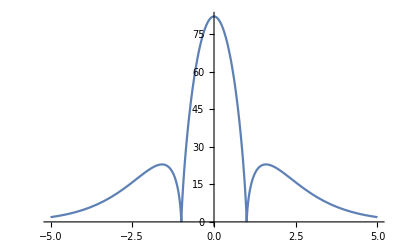

```mathematica
d = 1;
lam = 5;
Plot[120 Pi Abs[NIntegrate[Exp[I 2 Pi *Sqrt[x^2+d^2]/lam]/(2 lam Sqrt[x^2+d^2])  (d^2/(x^2+d^2)  + (I (d^2-2x^2))/((2 Pi/ lam)  *Sqrt[x^2+d^2]^3) -(d^2-2x^2)/((2 Pi/ lam)^2  *(x^2+d^2)^2)) Exp[I k *2*Pi/lam * x],{x,-∞,∞}]],{k,-5,5}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-13.0758}. NIntegrate obtained -4.6333×10^-14+6.73561×10^-18 ⅈ and 1.21487×10^-16 for the integral and error estimates.

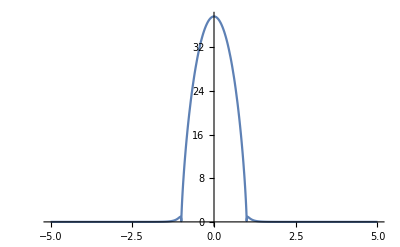

```mathematica
d = 5;
lam = 5;
Plot[120 Pi Abs[NIntegrate[Exp[I 2 Pi *Sqrt[x^2+d^2]/lam]/(2 lam Sqrt[x^2+d^2])  (d^2/(x^2+d^2)  + (I (d^2-2x^2))/((2 Pi/ lam)  *Sqrt[x^2+d^2]^3) -(d^2-2x^2)/((2 Pi/ lam)^2  *(x^2+d^2)^2)) Exp[I k *2*Pi/lam * x],{x,-∞,∞}]],{k,-5,5}]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {-12.5631}. NIntegrate obtained 2.98156×10^-18+5.67851×10^-18 ⅈ and 3.43546×10^-16 for the integral and error estimates.

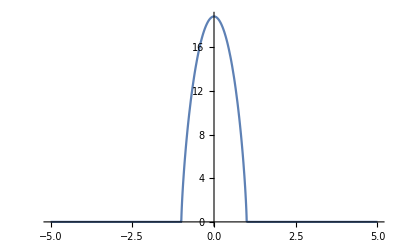

```mathematica
d = 20;
lam = 5;
Plot[120 Pi Abs[NIntegrate[Exp[I 2 Pi *Sqrt[x^2+d^2]/lam]/(2 lam Sqrt[x^2+d^2])  (d^2/(x^2+d^2)  + (I (d^2-2x^2))/((2 Pi/ lam)  *Sqrt[x^2+d^2]^3) -(d^2-2x^2)/((2 Pi/ lam)^2  *(x^2+d^2)^2)) Exp[I k *2*Pi/lam * x],{x,-∞,∞}]],{k,-5,5}]
```